```mathematica
(*
This notebook contains a symbolic demonstration for calculating the effective resistance between notes in a 3-cycle
according to the definition in the paper:
Chung,Fan,and Wenbo Zhao."Ranking and sparsifying a connection graph." International Workshop on Algorithms and Models for the Web-Graph.Berlin,Heidelberg:Springer Berlin Heidelberg,2012.

This notebook was written in Wolfram Mathematica 13.0. 

Please see the Github repository https://github.com/sawyer-jack-1/connection-resistance-demo for the license information and details.

*)
```

```mathematica
eye = {{1, 0}, {0, 1}};
zero = {{0, 0}, {0, 0}};
(* θ = Pi/2 *)
R[θ_] := {{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}; (*2x2 Rotation matrix*)
L [θ_] := ArrayFlatten[{{2*eye, -R[θ], -eye}, {-Transpose[R[θ]], 2*eye, -eye}, {-eye, -eye, 2*eye}}]; (*Connection laplacian matrix*)
```

```mathematica
P[θ_] := Simplify[Refine[PseudoInverse[L[θ]], { Element[θ, Reals], Element[θ, Interval[{0, 2*Pi}]]}]]; (*Simplified psuedoinverse of Connection laplacian matrix*)
B[θ_] := ArrayFlatten[{{R[θ], -eye, zero}, {eye, zero, -eye}, {zero, eye, -eye}}];(*Block incidence matrix Phi*)
F[s_] := Norm[Simplify[ B[s] . P[s] . Transpose[B[s]]][[1 ;; 2, 1 ;; 2]]]; (*Resistance value for angle s*)
```

```mathematica
Plot[F[s], {s, -Pi, Pi}] (*Cosing wave*)
```

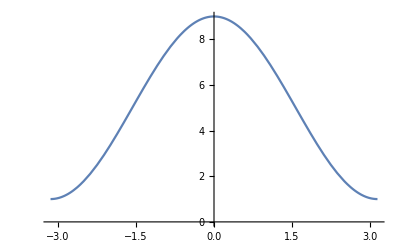

```mathematica
Simplify[F[0]] (*s = 2kpi for integers k corresponds w/ consistent graph. *)
```

```mathematica
2/3
```

```mathematica
FullSimplify[F[s],Assumptions->Element[s, Reals]] (*Mathematica is not detecting the discontinuity at zero*)
```

```mathematica
5+4 Cos[s]
```